```mathematica
SetDirectory["~/mthesis/graphanalysis"]
data=Import["data-unfiltered"];
T=2000+#[[1]]/12&/@data;
pkgs=#[[2]]&/@data;
newpkgs=#[[3]]&/@data;
delpkgs=#[[4]]&/@data;
deps=#[[5]]&/@data;
rev=#[[6]]&/@data;
```

/home/remco/UT/Vakken/410004 Master Thesis Business Administration/graphanalysis

```mathematica
dataAlsa=Import["test-data-alsa"]
```

{{95,1.25,0.538576},{96,1.28205,0.596946},{97,1.30128,0.654568},{98,1.35897,0.742041},{99,1.37179,0.778048},{100,1.40385,0.868087},{101,1.45513,1.1056},{102,1.53846,1.46928},{103,1.60897,1.75621},{104,1.62821,1.81947},{105,1.66667,1.85477},{106,1.77564,2.22046},{107,2.4359,4.68109},{108,2.45513,4.75737},{109,2.47436,4.82707},{110,2.52564,4.97229},{111,2.5641,5.04998},{112,2.55769,5.0195},{113,2.57051,5.06764},{114,2.57051,5.08027},{115,2.55128,5.07671},{116,2.5641,5.08162},{117,2.58333,5.0889},{118,2.61538,5.18561},{119,2.60256,5.1735},{120,2.60256,5.1735},{121,2.57692,5.10032},{122,2.74359,5.62489},{123,2.75,5.61434},{124,2.72436,5.56151},{125,2.75,5.61206},{126,2.74359,5.58371},{127,2.75,5.60406},{128,2.77564,5.67108},{129,0,0},{130,0,0},{131,0,0}}

```mathematica
P[l_]:=Inner[List,T,l,List][[8;;128]];
```

```mathematica
T6=dataAlsa⟦1;;-1,1;;2⟧;
```

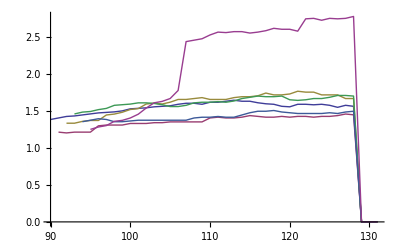

```mathematica
ListLinePlot[{T1,T2,T3,T4,T5,T6},PlotRange->Full]
```

```mathematica
PlotData[l_, opts:OptionsPattern[]]:=
ListLinePlot[P[l],
Filling->{1->0},
PlotStyle->Thickness[.003],
GridLines->{Automatic,None},
AxesOrigin->{2000,0},
FilterRules[{opts},Options[Plot]]
]
```

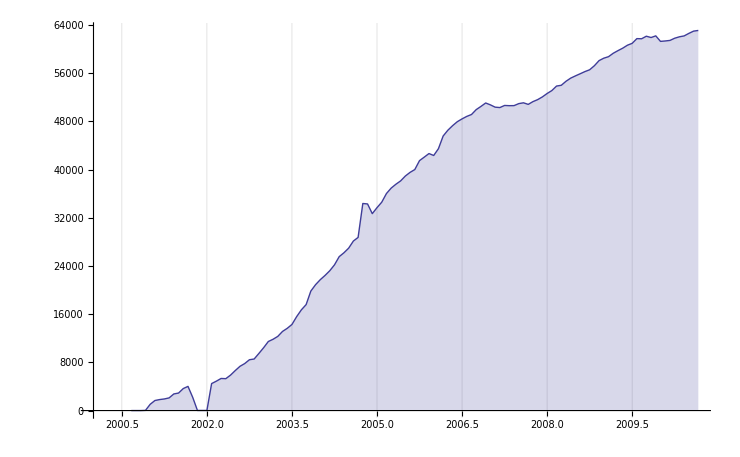

```mathematica
PlotData[deps]
```

```mathematica
Export["depsUnfiltered.pdf",%,ImageSize->300]
```

depsUnfiltered.pdf

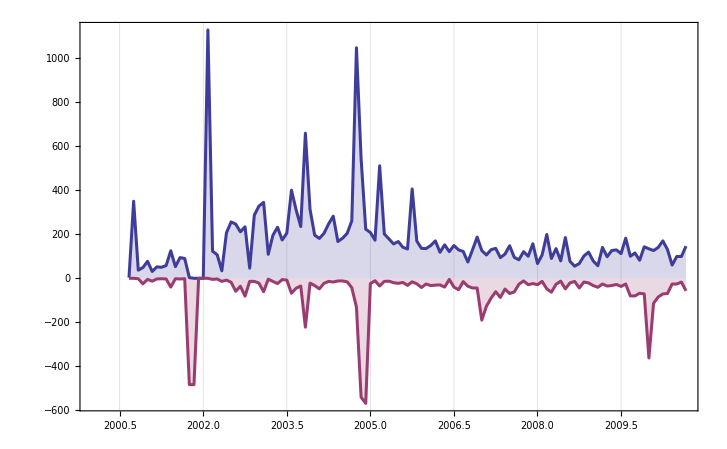

```mathematica
ListLinePlot[{P[newpkgs],P[-delpkgs]},
Filling->{1->0,2->0},
PlotStyle->Thickness[0.003],
GridLines->{Automatic,None},
AxesOrigin->{2000,-00},
PlotStyle->Thick,PlotRange->Full,Frame->True,FrameStyle->{{Black,White},{Black,White}},PlotRange->{{2000,2010.8},{-600,1200}},PlotRangeClipping->True]
```

```mathematica
Export["packageCountDeltaFiltered.pdf",%,ImageSize->300]
```

packageCountDeltaFiltered.pdf

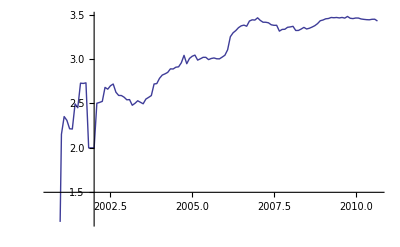

```mathematica
ListPlot[P[deps/pkgs],Joined->True]
```